```mathematica
list=ReadList["/home/san/Code/labs_comput/lab_3/interpol_uniform_grid_out.txt",{Real,Real}];

list1 = ReadList["/home/san/Code/labs_comput/lab_3/interpol_chebyshov_grid_out.txt",{Real,Real}];

list2=ReadList["/home/san/Code/labs_comput/lab_3/extrapol_out.txt",{Real,Real}];
list3=ReadList["/home/san/Code/labs_comput/lab_3/spline_out.txt",{Real,Real}];
```

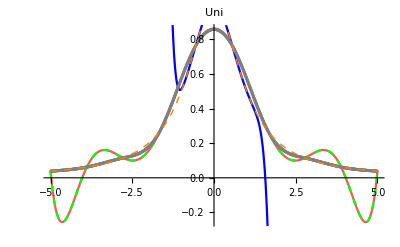

```mathematica
Show[ListLinePlot[list, PlotLabel->"Uni", PlotStyle->{Lighter@Red}],
ListLinePlot[list1, PlotLabel->"Cheb", PlotStyle->{Blue}],
ListLinePlot[list2, PlotLabel->"Extrapol", PlotStyle->{Green, Dashed}],
ListPlot[list3,PlotLabel->"Spline", PlotStyle->{Gray, Thick}],
Plot[1/(1+x^2),{x,-5,5}, PlotStyle->{Orange,Dashed, Thick}]]
```

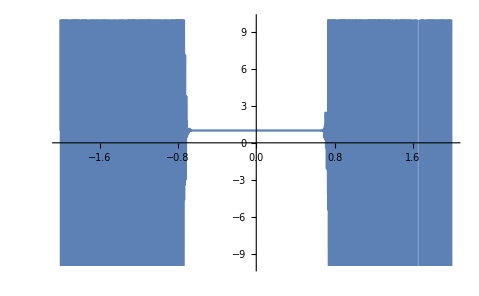
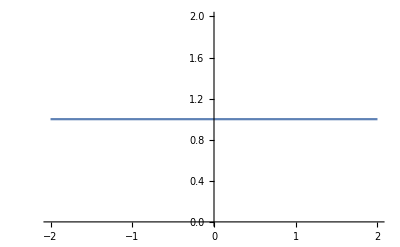

```mathematica
list=ReadList["/home/san/Code/labs_comput/lab_3/interpol_uniform_grid_out.txt",{Real,Real}];

list1 = ReadList["/home/san/Code/labs_comput/lab_3/interpol_chebyshov_grid_out.txt",{Real,Real}];
{ListLinePlot[list, PlotRange->{{-2,2},{-10,10}}], ListLinePlot[list1]}
```

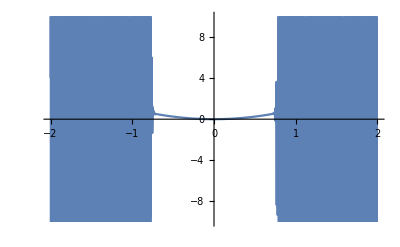
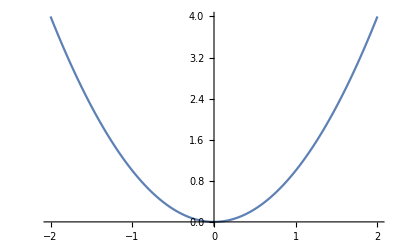

```mathematica
list=ReadList["/home/san/Code/labs_comput/lab_3/interpol_uniform_grid_out.txt",{Real,Real}];

list1 = ReadList["/home/san/Code/labs_comput/lab_3/interpol_chebyshov_grid_out.txt",{Real,Real}];
{ListLinePlot[list, PlotRange->{{-2,2},{-10,10}}], ListLinePlot[list1]}
```

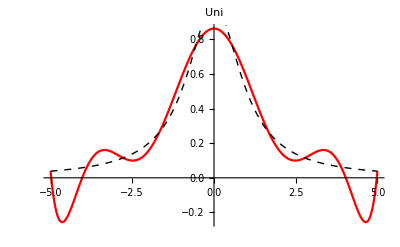

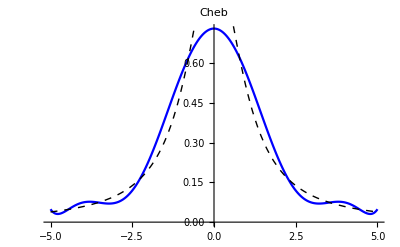

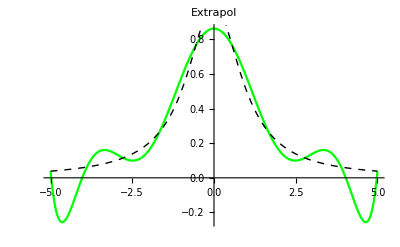

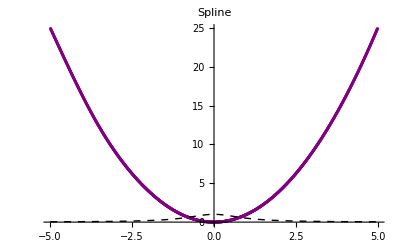

```mathematica
(*Show[ListLinePlot[list,PlotLabel->"Uni",PlotStyle->{Lighter@Red}],ListLinePlot[list1,PlotLabel->"Cheb",PlotStyle->{Blue}],ListLinePlot[list2,PlotLabel->"Extrapol",PlotStyle->{Green,Dashed}],ListPlot[list3,PlotLabel->"Spline",PlotStyle->{Gray,10}],Plot[1/(1+x^2),{x,-5,5},PlotStyle->{Orange,Dashed,Thick}]]*)Show[ListLinePlot[list,PlotLabel->"Uni",PlotStyle->{Red}],Plot[1/(1+x^2),{x,-5,5},PlotStyle->{Black,Dashed,Thick}]]

Show[ListLinePlot[list1,PlotLabel->"Cheb",PlotStyle->{Blue}],Plot[1/(1+x^2),{x,-5,5},PlotStyle->{Black,Dashed,Thick}]]

Show[ListLinePlot[list2,PlotLabel->"Extrapol",PlotStyle->{Green}],Plot[1/(1+x^2),{x,-5,5},PlotStyle->{Black,Dashed,Thick}]]

Show[ListPlot[list3,PlotLabel->"Spline",PlotStyle->{Purple,10}],Plot[1/(1+x^2),{x,-5,5},PlotStyle->{Black,Dashed,Thick}]]
```

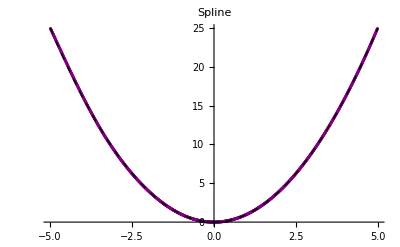

```mathematica
list3=ReadList["/home/san/Code/labs_comput/lab_3/spline_out.txt",{Real,Real}];
Show[ListPlot[list3,PlotLabel->"Spline",PlotStyle->{Purple,10}],Plot[x^2,{x,-5,5},PlotStyle->{Black,Dashed,Thick}]]
```